## Circuito Convencional 500kV

```mathematica
xy3={{-11.000,10.736},{-10.771,11.132},{-11.229,11.132},{0.000,10.736},{0.229,11.132},{-0.229,11.132},{11.000,10.736},{10.771,11.132},{11.229,11.132},{-6.000,22.000},{6.000,22.000}};;
```

```mathematica
mostra3={Circle[#,.25]}&/@xy3;
```

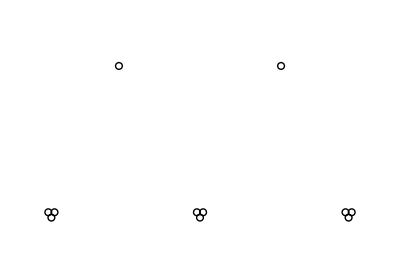

```mathematica
t3=Show[Graphics[mostra3],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{8,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

Dados do condutor de fase

```mathematica
rf=29.591*10^-3/2;
r0=(7.3914/2*10^-3);
ρc=6.114292531162*10^-5 Pi*(rf^2-r0^2);
```

Dados dos pára - raios

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
ρpr=Rdcpr*Pi*rpr^2;
```

Dados do solo

```mathematica
ρsolo=1000.;
σsolo=1/ρsolo;
```

Para o caso de cabos submarinos, considere o caso apresentado no arquivo 10pwrd02gustavsen.pdf